```mathematica
(*Mathematica*)
```

```mathematica
(*rational quadratic Pisot:GoldenRatio Analog:{1+Sqrt[17)/4,1-Sqrt[17)/4}*)
```

```mathematica
w0=x/.NSolve[x^2-x/2-1==0,x]
```

{-0.780776,1.28078}

```mathematica
Discriminant[x^2-x/2-1,x]
```

17/4

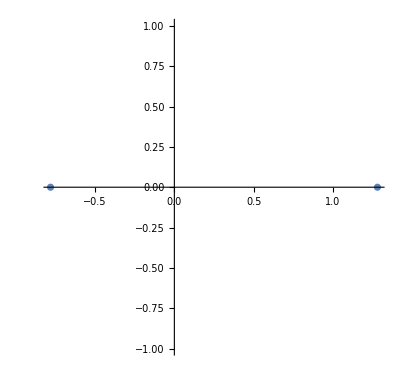

```mathematica
ComplexListPlot[w0,AspectRatio->Automatic]
```

```mathematica
Clear[a]
```

```mathematica
(* quadratic recursion function*)
```

```mathematica
a[0]=1;a[1]=1;
a[n_]:=a[n]=a[n-1]/2+a[n-2]
```

```mathematica
(* using powers of two to make an integer sequence:*)
```

```mathematica
w=Table[2^n*a[n],{n,0,100}]
```

{1,2,6,14,38,94,246,622,1606,4094,10518,26894,68966,176542,452406,1158574,2968198,7602494,19475286,49885262,127786406,327327454,838473078,2147782894,5501675206,14092806782,36099507606,92470734734,236868765158,606751704094,1554226764726,3981233581102,10198140640006,26123074964414,66915637524438,171407937382094,439070487479846,1124702237008222,2880984186927606,7379793134960494,18903729882670918,48422902422512894,124037821953196566,317729431643248142,813880719456034406,2084798446029026974,5340321323853164598,13679515107969272494,35040800403381930886,89758860835259020862,229922062448786744406,588957505789822827854,1508645755584969805478,3864475778744261116894,9899058801084140338806,25356961916061184806382,64953197120397746161606,166381044784642485387134,426193833266233470033558,1091718012404803411582094,2796493345469737291716326,7163365395088950938044702,18349338776967900104910006,47002800357323703857088814,120400155465195304276728838,308411356894490119705084094,790011978755271336811999446,2023657406333231815632335822,5183705321354317162880333606,13278334946687244425409676894,34013156232104513076931011318,87126496018853490778569718894,223179120947271543086293764166,571685105022685506200572639742,1464401588811771678545747696406,3751142008902513703348038255374,9608748364149600417531029040998,24613316399759655230923182062494,63048309856358056901047298226486,161501575455396677824740026476462,413694814880828905428929219382406,1059701116702415616727889325288254,2714480376225731238443606202817878,6953284843035393705355163503970894,17811206347938318659129588315242406,45624345720079893480550242331125982,116869171111833168117068595592095606,299366553992152742039269564916599534,766843238439485414507543947284981958,1964309454408096382664622206951380094,5031682408166038040694797996091307926,12888920225798423571353286823896828302,33015649858462575734132478808262060006,84571330761656270019545626103849373214,216633930195506572956075541336897613238,554919253242131653034258045752295106094,1421454974024157944858560211099885559046,3641131986992684556995592394109065983422,9326951883089316336429833238508608219606,23891479831060054564412202814944872153294,61199287363417319910131535768979305031718}

```mathematica
(*OEIS: https://oeis.org/A026597*)
```

```mathematica
(* Sequence function exists*)
```

```mathematica
f[n_]=FindSequenceFunction[w,n]
```

1+(4 (-68-68 √17-51 (1/2-(√17)/2)^n+5 √17 (1/2-(√17)/2)^n+68 (1/2+(√17)/2)^n+12 √17 (1/2+(√17)/2)^n))/(17 (-1+√17) (1+√17)^2)

```mathematica
Table[FullSimplify[f[n]],{n,20}]
```

{1,2,6,14,38,94,246,622,1606,4094,10518,26894,68966,176542,452406,1158574,2968198,7602494,19475286,49885262}

```mathematica
(* generating function exists*)
```

```mathematica
g[x_]=FindGeneratingFunction[w,x]
```

(-1-x)/(-1+x+4 x^2)

```mathematica
CoefficientList[Normal[Series[g[x],{x,0,100}]],x]
```

{1,2,6,14,38,94,246,622,1606,4094,10518,26894,68966,176542,452406,1158574,2968198,7602494,19475286,49885262,127786406,327327454,838473078,2147782894,5501675206,14092806782,36099507606,92470734734,236868765158,606751704094,1554226764726,3981233581102,10198140640006,26123074964414,66915637524438,171407937382094,439070487479846,1124702237008222,2880984186927606,7379793134960494,18903729882670918,48422902422512894,124037821953196566,317729431643248142,813880719456034406,2084798446029026974,5340321323853164598,13679515107969272494,35040800403381930886,89758860835259020862,229922062448786744406,588957505789822827854,1508645755584969805478,3864475778744261116894,9899058801084140338806,25356961916061184806382,64953197120397746161606,166381044784642485387134,426193833266233470033558,1091718012404803411582094,2796493345469737291716326,7163365395088950938044702,18349338776967900104910006,47002800357323703857088814,120400155465195304276728838,308411356894490119705084094,790011978755271336811999446,2023657406333231815632335822,5183705321354317162880333606,13278334946687244425409676894,34013156232104513076931011318,87126496018853490778569718894,223179120947271543086293764166,571685105022685506200572639742,1464401588811771678545747696406,3751142008902513703348038255374,9608748364149600417531029040998,24613316399759655230923182062494,63048309856358056901047298226486,161501575455396677824740026476462,413694814880828905428929219382406,1059701116702415616727889325288254,2714480376225731238443606202817878,6953284843035393705355163503970894,17811206347938318659129588315242406,45624345720079893480550242331125982,116869171111833168117068595592095606,299366553992152742039269564916599534,766843238439485414507543947284981958,1964309454408096382664622206951380094,5031682408166038040694797996091307926,12888920225798423571353286823896828302,33015649858462575734132478808262060006,84571330761656270019545626103849373214,216633930195506572956075541336897613238,554919253242131653034258045752295106094,1421454974024157944858560211099885559046,3641131986992684556995592394109065983422,9326951883089316336429833238508608219606,23891479831060054564412202814944872153294,61199287363417319910131535768979305031718}

```mathematica
(* Limiting ratio of the power two sequence*)
```

```mathematica
Table[N[w[[n+1]]/w[[n]]],{n,Length[w]-1}]
```

{2.,3.,2.33333,2.71429,2.47368,2.61702,2.52846,2.58199,2.54919,2.56913,2.55695,2.56436,2.55984,2.5626,2.56092,2.56194,2.56132,2.5617,2.56146,2.56161,2.56152,2.56157,2.56154,2.56156,2.56155,2.56156,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155,2.56155}

```mathematica
%/1.2807764064044151
```

{1.56155,2.34233,1.82181,2.11925,1.93139,2.04331,1.97416,2.01596,1.99035,2.00591,1.99641,2.00219,1.99866,2.00082,1.9995,2.0003,1.99982,2.00011,1.99993,2.00004,1.99997,2.00002,1.99999,2.00001,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}

```mathematica
(* rational sequence*)
```

```mathematica
Table[2*a[n+1]/(a[n]),{n,0,10}]
```

{2,3,7/3,19/7,47/19,123/47,311/123,803/311,2047/803,5259/2047,13447/5259}

```mathematica
(* Limiting ratio of the recursion*)
```

```mathematica
Table[N[a[n+1]/a[n]],{n,0,100}]
```

{1.,1.5,1.16667,1.35714,1.23684,1.30851,1.26423,1.291,1.2746,1.28456,1.27847,1.28218,1.27992,1.2813,1.28046,1.28097,1.28066,1.28085,1.28073,1.2808,1.28076,1.28079,1.28077,1.28078,1.28077,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078,1.28078}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(*rational cubic Pisot: minimal Pisot Analog*)
```

```mathematica
w0=x/.NSolve[x^3-x/2-1==0,x]
```

{-0.582687-0.720119 ⅈ,-0.582687+0.720119 ⅈ,1.16537}

```mathematica
Abs[w]
```

{0.926334,0.926334,1.16537}

```mathematica
(*Weirstrass elliptc function:w^2=4*x^3-2x-4*)
```

```mathematica
g2=2;g3=4;
```

```mathematica
j=g2^3/(g2^3-27*g3^2)
```

-1/53

```mathematica
Discriminant[x^3-x/2-1,x]
```

-53/2

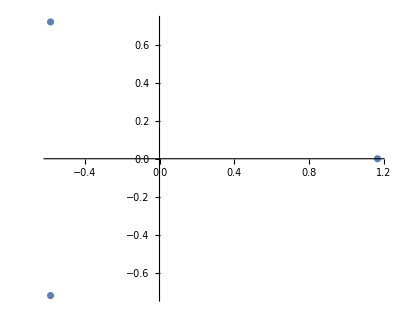

```mathematica
ComplexListPlot[w0,AspectRatio->Automatic]
```

```mathematica
Clear[a]
```

```mathematica
(* cubic recursion function*)
```

```mathematica
a[0]=1;a[1]=1;a[2]=1;
a[n_]:=a[n]=a[n-2]/2+a[n-3]
```

```mathematica
(* using powers of two to make an integer sequence:*)
```

```mathematica
w=Table[2^n*a[n],{n,0,100}]
```

{1,2,4,12,24,56,144,304,736,1760,3904,9408,21888,50048,119040,275200,638464,1502720,3478528,8113152,18978816,44054528,102862848,239939584,558161920,1302781952,3035840512,7070859264,16493936640,38428442624,89554747392,208808378368,486537035776,1134054735872,2643541098496,6160405757952,14359520083968,33469140303872,78002286231552,181814441279488,423757694894080,987647172411392,2302030920024064,5365355903975424,12505239219339264,29146959168143360,67933325670481920,158335832091000832,369042324686110720,860138269545857024,2004771306100228096,4672615136580599808,10890648768567312384,25383400721963024384,59162218629779423232,137891991592464547840,321391643035263041536,749081732223164481536,1745919218810242465792,4069296608728433295360,9484492295405800783872,22105946967938806317056,51523357460639067930624,120087832299124018905088,279894290664788586397696,652362524283360581255168,1520491239722569324036096,3543879373885029853691904,8259882673712023298113536,19251688665550614299672576,44870800338504285425762304,104582438720797414984253440,243755110001413485248905216,568131280149629113374605312,1324169729769206290371837952,3086303440310566108740452352,7193389700735445487740518400,16765964718774782540455608320,39077206923955419845404655616,91079047043433128982835363840,212282131598109100014454177792,494775749478509616728907972608,1153196639543683231891591266304,2687808551741892033573449367552,6264599274915443397614446313472,14601190219833249922279628865536,34031666963766023063816487567360,79319174638990047025474828238848,184872855686198045505870006059008,430891684988108278561481557016576,1004299108484316467215538638028800,2340766215465800921169923162505216,5455731696873499162922929732190208,12715925298806133580064155429240832,29637593117473405695205244764422144,69077704172600260463511748716003328,161002588625395880030923732962770944,375256153284987766488665455547383808,874626810631593843769941455653568512,2038533015573142573224720774796935168,4751302847543089819449206555686207488}

```mathematica
(* OEIS: Search:seq:1,2,4,12,24,56,144,304,736,1760,3904

Sorry,but the terms do not match anything in the table.*)
```

```mathematica
(* Sequence function exists*)
```

```mathematica
f[n_]=FindSequenceFunction[w,n]
```

(Root2.33Root[-8-2 #1+#1^3&,1]2.3307460861248295)^n Root0.363Root[-1-32 #1-212 #1^2+848 #1^3&,1]0.3629287630785754+(Root-1.17+1.44 ⅈRoot[-8-2 #1+#1^3&,3]-1.1653730430624147)^n Root-0.0565-7.81 × 10^-3 ⅈRoot[-1-32 #1-212 #1^2+848 #1^3&,2]-0.05646438153928769+(Root-1.17-1.44 ⅈRoot[-8-2 #1+#1^3&,2]-1.1653730430624147)^n Root-0.0565+7.81 × 10^-3 ⅈRoot[-1-32 #1-212 #1^2+848 #1^3&,3]-0.05646438153928769

```mathematica
N[(Root"2.33"Root[-8-2 #1+#1^3&,1]2.3307460861248295)^n Root"0.363"Root[-1-32 #1-212 #1^2+848 #1^3&,1]0.3629287630785754+(Root"-1.17"+"1.44" ⅈRoot[-8-2 #1+#1^3&,3]-1.1653730430624147)^n Root"-0.0565"-"7.81"" × "("10")^("-3") ⅈRoot[-1-32 #1-212 #1^2+848 #1^3&,2]-0.05646438153928769+(Root"-1.17"-"1.44" ⅈRoot[-8-2 #1+#1^3&,2]-1.1653730430624147)^n Root"-0.0565"+"7.81"" × "("10")^("-3") ⅈRoot[-1-32 #1-212 #1^2+848 #1^3&,3]-0.05646438153928769]
```

(-0.0564644+0.00781159 ⅈ) (-1.16537-1.44024 ⅈ)^n-(0.0564644+0.00781159 ⅈ) (-1.16537+1.44024 ⅈ)^n+0.362929 2.33075^n

```mathematica
Table[FullSimplify[f[n]],{n,20}]
```

{1,2,4,12,24,56,144,304,736,1760,3904,9408,21888,50048,119040,275200,638464,1502720,3478528,8113152}

```mathematica
(* generating function exists*)
```

```mathematica
g[x_]=FindGeneratingFunction[w,x]
```

(-1-2 x-2 x^2)/(-1+2 x^2+8 x^3)

```mathematica
CoefficientList[Normal[Series[g[x],{x,0,100}]],x]
```

{1,2,4,12,24,56,144,304,736,1760,3904,9408,21888,50048,119040,275200,638464,1502720,3478528,8113152,18978816,44054528,102862848,239939584,558161920,1302781952,3035840512,7070859264,16493936640,38428442624,89554747392,208808378368,486537035776,1134054735872,2643541098496,6160405757952,14359520083968,33469140303872,78002286231552,181814441279488,423757694894080,987647172411392,2302030920024064,5365355903975424,12505239219339264,29146959168143360,67933325670481920,158335832091000832,369042324686110720,860138269545857024,2004771306100228096,4672615136580599808,10890648768567312384,25383400721963024384,59162218629779423232,137891991592464547840,321391643035263041536,749081732223164481536,1745919218810242465792,4069296608728433295360,9484492295405800783872,22105946967938806317056,51523357460639067930624,120087832299124018905088,279894290664788586397696,652362524283360581255168,1520491239722569324036096,3543879373885029853691904,8259882673712023298113536,19251688665550614299672576,44870800338504285425762304,104582438720797414984253440,243755110001413485248905216,568131280149629113374605312,1324169729769206290371837952,3086303440310566108740452352,7193389700735445487740518400,16765964718774782540455608320,39077206923955419845404655616,91079047043433128982835363840,212282131598109100014454177792,494775749478509616728907972608,1153196639543683231891591266304,2687808551741892033573449367552,6264599274915443397614446313472,14601190219833249922279628865536,34031666963766023063816487567360,79319174638990047025474828238848,184872855686198045505870006059008,430891684988108278561481557016576,1004299108484316467215538638028800,2340766215465800921169923162505216,5455731696873499162922929732190208,12715925298806133580064155429240832,29637593117473405695205244764422144,69077704172600260463511748716003328,161002588625395880030923732962770944,375256153284987766488665455547383808,874626810631593843769941455653568512,2038533015573142573224720774796935168,4751302847543089819449206555686207488}

```mathematica
(* Limiting ratio of the power two sequence*)
```

```mathematica
Table[N[w[[n+1]]/w[[n]]],{n,Length[w]-1}]
```

{2.,2.,3.,2.,2.33333,2.57143,2.11111,2.42105,2.3913,2.21818,2.40984,2.32653,2.28655,2.37852,2.31183,2.32,2.35365,2.31482,2.33235,2.33927,2.32125,2.3349,2.33262,2.32626,2.33406,2.33028,2.32913,2.33266,2.32985,2.33043,2.33163,2.33006,2.33087,2.33105,2.33036,2.33094,2.3308,2.33057,2.33089,2.33072,2.33069,2.33082,2.33071,2.33074,2.33078,2.33072,2.33075,2.33076,2.33073,2.33075,2.33075,2.33074,2.33075,2.33074,2.33074,2.33075,2.33074,2.33075,2.33075,2.33074,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075,2.33075}

```mathematica
%/1.1653730430624147
```

{1.71619,1.71619,2.57428,1.71619,2.00222,2.20653,1.81153,2.07749,2.05196,1.90341,2.06787,1.99638,1.96208,2.04099,1.98377,1.99078,2.01965,1.98633,2.00138,2.00731,1.99185,2.00356,2.00161,1.99615,2.00284,1.9996,1.99861,2.00165,1.99923,1.99973,2.00076,1.99942,2.00011,2.00026,1.99967,2.00016,2.00004,1.99985,2.00012,1.99997,1.99995,2.00007,1.99997,1.99999,2.00003,1.99998,2.00001,2.00001,1.99999,2.00001,2.,1.99999,2.00001,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}

```mathematica
(*rational sequence*)
```

```mathematica
Table[2*a[n+1]/(a[n]),{n,0,10}]
```

{2,2,3,2,7/3,18/7,19/9,46/19,55/23,122/55,147/61}

```mathematica
(* Limiting ratio of the recursion*)
```

```mathematica
Table[N[a[n+1]/a[n]],{n,0,100}]
```

{1.,1.,1.5,1.,1.16667,1.28571,1.05556,1.21053,1.19565,1.10909,1.20492,1.16327,1.14327,1.18926,1.15591,1.16,1.17682,1.15741,1.16618,1.16963,1.16062,1.16745,1.16631,1.16313,1.16703,1.16514,1.16456,1.16633,1.16493,1.16521,1.16581,1.16503,1.16544,1.16553,1.16518,1.16547,1.1654,1.16529,1.16544,1.16536,1.16534,1.16541,1.16535,1.16537,1.16539,1.16536,1.16538,1.16538,1.16537,1.16538,1.16537,1.16537,1.16538,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537,1.16537}

```mathematica
(*end*)
```